```mathematica
Integrate[x Sin[x*r]/(1+x^2/Λ^2),{x,0,Infinity}]
Integrate[x Exp[-x^2/Λ^2]*Sin[x*r],{x,0,Infinity}]
```

ConditionalExpression[(ⅇ^(-Abs[r]/(√(1/Λ^2))) π r Λ^2)/(2 Abs[r]), r∈ℝ&&(Re[Λ^2]≥0||Λ^2∉ℝ)]

ConditionalExpression[(ⅇ^(-1/4 r^2 Λ^2) √π r)/(4 (1/Λ^2)^(3/2)), Re[Λ^2]>0]

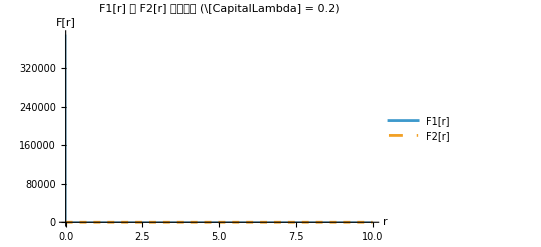

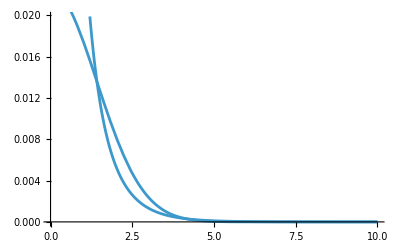

```mathematica
F1[r_]:=1/(2Pi^2r)(ⅇ^(-(√(r^2))/(√(1/Λ^2))) π r Λ^2)/(2 √(r^2)) /. Λ->1
F2[r_]:=1/(2Pi^2r) (ⅇ^(-1/4 r^2 Λ^2) √π r)/(4 (1/Λ^2)^(3/2))/. Λ->1
Plot[{F1[r],F2[r]},{r,0,10},PlotRange->All,PlotLegends->{"F1[r]","F2[r]"},PlotStyle->{Thick,Dashed},AxesLabel->{"r","F[r]"},PlotLabel->"F1[r] 與 F2[r] 的比較圖 (\\[CapitalLambda] = 0.2)" ]
```